```mathematica
SetDirectory[NotebookDirectory[]<>"data.06"]
```

F:\Загрузки\Диплом\Real_Sig\data.06

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
data=Import["v2k_bpm_xy_1.sdds","Table","HeaderLines"->13];
Data1 = Transpose[data][[3]]
Data1 = Take[Data1, {1,100}]
```

{-0.526478,-0.516873,-0.520342,-0.517408,-0.518347,-0.516276,-0.521875,-0.517675,-0.514209,-0.522277,-0.519746,-0.522546,-0.517538,-0.52268,-0.521875,-0.524807,8157,-0.518075,-0.516808,-0.515535,-0.521414,-0.517805,-0.513591,-0.517941,-0.514468,-0.507595,-0.519609,-0.518208,-0.518611,-0.516404,-0.511802,-0.516675,-0.519475}
 |  |  |  |

{-0.526478,-0.516873,-0.520342,-0.517408,-0.518347,-0.516276,-0.521875,-0.517675,-0.514209,-0.522277,-0.519746,-0.522546,-0.517538,-0.52268,-0.521875,-0.524807,-0.520206,-0.522278,-0.523082,-0.521145,-0.525077,-0.523813,-0.519344,-0.519344,-0.515337,-0.524216,-0.517139,-0.466094,-0.343287,-0.340882,-0.531399,-0.717931,-0.605501,-0.385637,-0.307522,-0.513396,-1.14834,-1.39568,-0.649096,0.132384,-0.074024,-0.967209,-1.40614,-0.918631,-0.128844,-0.046113,-0.587173,-0.966908,-0.78818,-0.405499,-0.317742,-0.493939,-0.594628,-0.568777,-0.560821,-0.608578,-0.561621,-0.415909,-0.370019,-0.530877,-0.723131,-0.679646,-0.449339,-0.321602,-0.427463,-0.631143,-0.696943,-0.593645,-0.443983,-0.379002,-0.444474,-0.594676,-0.697922,-0.65562,-0.458226,-0.313227,-0.416713,-0.659497,-0.775115,-0.609923,-0.350639,-0.296782,-0.500014,-0.739477,-0.725936,-0.514489,-0.330419,-0.366406,-0.563605,-0.712907,-0.682269,-0.507613,-0.360953,-0.384689,-0.569554,-0.722143,-0.684613,-0.480948,-0.332158,-0.399812}

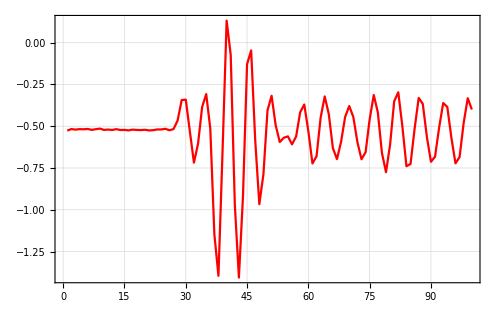

```mathematica
ListLinePlot[Data1]
```

```mathematica
NAFF[x_]:=Abs[Table[Sum[x[[n]]*Exp[ⅈ*2π*β*n],{n,1,Length[x]}],{β,0,1,0.0001}]]
Nf[x_]:=Take[NAFF[x],{1000,5000}]
```

```mathematica
NumPlaceNAFF[x_]:=Position[Nf[x],Max[Nf[x]]][[1,1]]
FreqListNAFF[x_]:=Table[1.0*b/10000,{b,0,10000}]
Freql[x_]:=Take[FreqListNAFF[x],{1000,5000}]
```

```mathematica
FreqNAFF[x_]:=Freql[x][[NumPlaceNAFF[x]]]
```

```mathematica
TruePlotNAFF[x_]:=ListPlot[Transpose[{FreqListNAFF[x],NAFF[x]}],FrameLabel->{"ν","A, mm"}]
```

0.1692

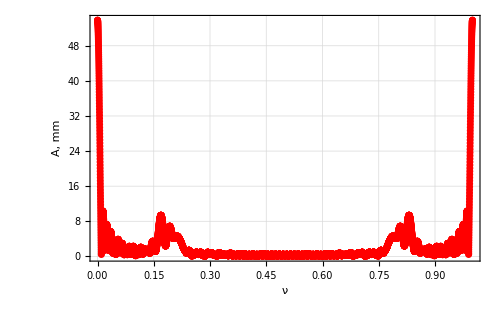

```mathematica
nf=Take[NAFF[Data1],{1000,5000}];
FreqNAFF[Data1]
TruePlotNAFF[Data1]
```